# Cálculo de pârametros unitários de uma linha de transmissão

## Antonio Carlos S Lima EEE457 - Transmissão de Energia Elétrica 2021/1

## Início

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\anton\Dropbox\UFRJ\cursos\EEE457-Transmissão_Energia_Elétrica\arquivos_Mma_EEE457

### Algumas constantes

```mathematica
μ= 4.0 π 10^-7;
ϵ= 8.854 10^-12;
σs=10.0^-3;
ℓ=80 10^3; (* comprimento do circuito *)
```

cabos pararraios possuem permeabilidade magnética relativa próximo a 100

```mathematica
μr= 90.0;
```

## Circuito 138kV

Coordenadas dos condutores

```mathematica
xc={-4,-4,-4,4,4,4,-4.5,4.5};
yc={37.35,31.35,25.35,25.35,31.35, 37.35,42.05,42.05};
```

Dados condutores de fase

```mathematica
rf=0.013265;
rint=7.05*10^-3;
Rdc=0.0007998;
```

Dados dos cabos pararraios

```mathematica
rpr=4.57*10^-3;
Rdcpr=4.19*10^-3;
```

```mathematica
mostra=Table[{Circle[{xc[[i]],yc[[i]]},{0.09,0.20}]},{i,1,Length[xc]}];
o1=tsimples=Show[Graphics[mostra],Axes->False,Frame->Automatic,AspectRatio-> 0.5,PlotRange->{{-5,5},{5,50.}},BaseStyle->{FontFamily->"Helvetica", 14},ImageSize-> 600,FrameLabel->{Style["Distance [m]",Bold,18],Style["Distance [m]",Bold,18]}]
```

-Graphics-

## Função para cálculo das matrizes

faz parte do arquivo LineCableParam2020.wl

```mathematica
(* impedancia interna de condutores tubulares *)
ZintTubo[Omega_, Rhoc_, rf_, rint_, Mur_: 1, Mu_: (4.*Pi)/10^7] := 
 With[{Etac = N[Sqrt[(I*Omega*Mur*Mu)/Rhoc]], ri = rint + 10^-6}, 
  With[{Den = 
     BesselK[1, Etac*ri]*BesselI[1, Etac*rf] - 
      BesselK[1, Etac*rf]*BesselI[1, Etac*ri], 
    Num = BesselK[1, Etac*ri]*BesselI[0, Etac*rf] + 
      BesselK[0, Etac*rf]*BesselI[1, Etac*ri]}, ((Rhoc*Etac)*
      Num)/((2*Pi*rf)*Den)]]
      
(* impedancia interna de condutor sem alma de aco *)
(* impedancia interna de condutores cilindricos *) 
(*Mur=90 para cables de aco*)    
Zin[Omega_, Rhopr_, rpr_, Mur_:90, Mu_:(4*Pi)/10^7] := 
    With[{Etapr = Sqrt[(I*Omega*Mu*Mur)/Rhopr]}, 
         ((Etapr*Rhopr)*BesselI[0, Etapr*rpr])/((2*Pi*rpr)*BesselI[1,Etapr*rpr])]
```

```mathematica
(* internal impedance of cylindrical conductors *)
zintc= Compile[{{omega, _Complex}, {Rhoc, _Real}, {rf, _Real}, {ri,_Real}, {Mur, _Real}},
 ZintTubo[omega, Rhoc, rf, ri, Mur]];
 
zic= Compile[{{omega,_Complex},{rhoc, _Real},{rf, _Real}, {mur,_Real}},
	 Zin[omega, rhoc, rf, mur]];
```

```mathematica
(*  ground wires are not explicitly considered so we include their effects via Kron Reduction -- matrizes devem estar no formato de impedancia *)        
eliprc = Compile[{{m,_Complex,2},{nc,_Integer},{np,_Integer}},
	            Take[Inverse[m], nc - np, nc - np]
	            ];
```

```mathematica
(* case  2: ground wires and unbundled conductors *)
cZYlt[omega_,(x_)?VectorQ, (y_)?VectorQ, sigmas_, rdc_,rf_,rint_, npr_, rdcpr_, rpr_]:=
    Module[{mu=4*Pi*10^-7, eps=8.854*10^-12, nc=Length[x],  nf, rhoc, rhopr, mp, zin, ze, Z1, Y1},
    	
    nf= IntegerPart[(nc-npr)];
    rhoc= rdc*Pi*(rf^2-rint^2);
    rhopr= rdcpr*Pi*rpr^2;
   
   If[ rint != 0, 
   zin= DiagonalMatrix[
   	    Join[zintc[omega, rhoc, rf, rint, 1] Table[1, {i, nc - npr}], 
             zic[omega, rhopr, rpr, 90] Table[1, {i, npr}]]
             ],
   zin= DiagonalMatrix[
   	    Join[zic[omega, rhoc, rf, 1] Table[1, {i, nc - npr}], 
             zic[omega, rhopr, rpr,90] Table[1, {i, npr}]]
             ];
   ];
   
             
   ze= I omega mu/(2 Pi) With[{p = Sqrt[1/(I*omega*mu*sigmas)]}, 
         Table[If[i != j, 
         	  (Log[((x[[i]] - x[[j]])^2 + (2*p + y[[i]] + y[[j]])^2)/((x[[i]] - x[[j]])^2 +(y[[i]] - y[[j]])^2)])/(2), 
              If[i <= nc - npr, 
               (Log[(2*(y[[i]] + p))/rf]), 
               (Log[(2*(y[[i]] + p))/rpr])]],
         {i, 1, nc}, 
         {j, 1, nc}]];
         
    Z1 = Inverse[eliprc[zin+ze, nc, npr]];     
         
    mp= Table[If[i != j, 
   	    (1/2)*Log[((x[[i]] - x[[j]])^2 + (y[[i]] + y[[j]])^2)/((x[[i]] - x[[j]])^2 + (y[[i]] - y[[j]])^2)], 
        If[i <= nc - npr, Log[(2*y[[i]])/rf], 
        Log[(2*y[[i]])/rpr]]],{i, 1, nc}, {j, 1, nc}];
          
    Y1=3.0*10^-12 DiagonalMatrix[Table[1,{nf}]] + I omega*2*Pi*eps* eliprc[mp, nc, npr];
          
    {Z1, Y1}       
];
```

## Cálculo das matrizes

```mathematica
ω= 2. π 60;
ρs= 1000.;
npr = 2;
```

```mathematica
{Zmat, Ymat} =cZYlt[ω,xc,yc,1/ρs, Rdc,rf,rint, npr, Rdcpr, rpr];
```

```mathematica
MatrixForm[Zmat 1000]
```

(0.909393+0.881242 ⅈ | 0.103855+0.413703 ⅈ | 0.100276+0.36456 ⅈ | 0.100191+0.35074 ⅈ | 0.103675+0.375279 ⅈ | 0.108928+0.387414 ⅈ
0.103855+0.413703 ⅈ | 0.898878+0.890525 ⅈ | 0.0957797+0.420964 ⅈ | 0.0957507+0.382463 ⅈ | 0.0988851+0.396459 ⅈ | 0.103675+0.375279 ⅈ
0.100276+0.36456 ⅈ | 0.0957797+0.420964 ⅈ | 0.892804+0.896043 ⅈ | 0.0928585+0.401952 ⅈ | 0.0957507+0.382463 ⅈ | 0.100191+0.35074 ⅈ
0.100191+0.35074 ⅈ | 0.0957507+0.382463 ⅈ | 0.0928585+0.401952 ⅈ | 0.892804+0.896043 ⅈ | 0.0957797+0.420964 ⅈ | 0.100276+0.36456 ⅈ
0.103675+0.375279 ⅈ | 0.0988851+0.396459 ⅈ | 0.0957507+0.382463 ⅈ | 0.0957797+0.420964 ⅈ | 0.898878+0.890525 ⅈ | 0.103855+0.413703 ⅈ
0.108928+0.387414 ⅈ | 0.103675+0.375279 ⅈ | 0.100191+0.35074 ⅈ | 0.100276+0.36456 ⅈ | 0.103855+0.413703 ⅈ | 0.909393+0.881242 ⅈ)

```mathematica
MatrixForm[Ymat 1000]
```

(3.×10^-9+3.00434×10^-6 ⅈ | 0.-4.76501×10^-7 ⅈ | 0.-2.0134×10^-7 ⅈ | 0.-1.34033×10^-7 ⅈ | 0.-2.30235×10^-7 ⅈ | 0.-3.29885×10^-7 ⅈ
0.-4.76501×10^-7 ⅈ | 3.×10^-9+3.0061×10^-6 ⅈ | 0.-5.01396×10^-7 ⅈ | 0.-2.49002×10^-7 ⅈ | 0.-3.15975×10^-7 ⅈ | 0.-2.30235×10^-7 ⅈ
0.-2.0134×10^-7 ⅈ | 0.-5.01396×10^-7 ⅈ | 3.×10^-9+2.91641×10^-6 ⅈ | 0.-3.87974×10^-7 ⅈ | 0.-2.49002×10^-7 ⅈ | 0.-1.34033×10^-7 ⅈ
0.-1.34033×10^-7 ⅈ | 0.-2.49002×10^-7 ⅈ | 0.-3.87974×10^-7 ⅈ | 3.×10^-9+2.91641×10^-6 ⅈ | 0.-5.01396×10^-7 ⅈ | 0.-2.0134×10^-7 ⅈ
0.-2.30235×10^-7 ⅈ | 0.-3.15975×10^-7 ⅈ | 0.-2.49002×10^-7 ⅈ | 0.-5.01396×10^-7 ⅈ | 3.×10^-9+3.0061×10^-6 ⅈ | 0.-4.76501×10^-7 ⅈ
0.-3.29885×10^-7 ⅈ | 0.-2.30235×10^-7 ⅈ | 0.-1.34033×10^-7 ⅈ | 0.-2.0134×10^-7 ⅈ | 0.-4.76501×10^-7 ⅈ | 3.×10^-9+3.00434×10^-6 ⅈ)

```mathematica
r={{0,1,0},{0,0,1},{1,0,0}};
r1={{0,0,1},{1,0,0},{0,1,0}};
transp=ArrayFlatten[{{r,0},{0,r1}}];
MatrixForm[transp]
```

(0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0)

```mathematica
a= Exp[I 120 Degree];
A={{1,1,1},{1,a^2,a},{1,a,a^2}};
Aplus=ArrayFlatten[{{A,0},{0,A}}];
MatrixForm[Aplus]
```

(1 | 1 | 1 | 0 | 0 | 0
1 | ⅇ^(240 ⅈ °) | ⅇ^(120 ⅈ °) | 0 | 0 | 0
1 | ⅇ^(120 ⅈ °) | ⅇ^(240 ⅈ °) | 0 | 0 | 0
0 | 0 | 0 | 1 | 1 | 1
0 | 0 | 0 | 1 | ⅇ^(240 ⅈ °) | ⅇ^(120 ⅈ °)
0 | 0 | 0 | 1 | ⅇ^(120 ⅈ °) | ⅇ^(240 ⅈ °))

```mathematica
MatrixForm[zfinal=(Zmat +Inverse[transp].Zmat .transp+ Inverse[transp].( Inverse[transp].Zmat .transp).transp)/3]
```

(0.000900358+0.00088927 ⅈ | 0.0000999703+0.000399742 ⅈ | 0.0000999703+0.000399742 ⅈ | 0.000099872+0.000369494 ⅈ | 0.000099872+0.000369494 ⅈ | 0.000100224+0.000395275 ⅈ
0.0000999703+0.000399742 ⅈ | 0.000900358+0.00088927 ⅈ | 0.0000999703+0.000399742 ⅈ | 0.000099872+0.000369494 ⅈ | 0.000100224+0.000395275 ⅈ | 0.000099872+0.000369494 ⅈ
0.0000999703+0.000399742 ⅈ | 0.0000999703+0.000399742 ⅈ | 0.000900358+0.00088927 ⅈ | 0.000100224+0.000395275 ⅈ | 0.000099872+0.000369494 ⅈ | 0.000099872+0.000369494 ⅈ
0.000099872+0.000369494 ⅈ | 0.000099872+0.000369494 ⅈ | 0.000100224+0.000395275 ⅈ | 0.000900358+0.00088927 ⅈ | 0.0000999703+0.000399742 ⅈ | 0.0000999703+0.000399742 ⅈ
0.000099872+0.000369494 ⅈ | 0.000100224+0.000395275 ⅈ | 0.000099872+0.000369494 ⅈ | 0.0000999703+0.000399742 ⅈ | 0.000900358+0.00088927 ⅈ | 0.0000999703+0.000399742 ⅈ
0.000100224+0.000395275 ⅈ | 0.000099872+0.000369494 ⅈ | 0.000099872+0.000369494 ⅈ | 0.0000999703+0.000399742 ⅈ | 0.0000999703+0.000399742 ⅈ | 0.000900358+0.00088927 ⅈ)

```mathematica
z012=1000Chop@FullSimplify[Inverse[Aplus].zfinal.Aplus];
MatrixForm[z012]
```

(1.1003+1.68875 ⅈ | 0 | 0 | 0.299968+1.13426 ⅈ | 0 | 0
0 | 0.800388+0.489528 ⅈ | 0 | 0 | 0 | 0.0221513-0.0131952 ⅈ
0 | 0 | 0.800388+0.489528 ⅈ | 0 | -0.022503-0.012586 ⅈ | 0
0.299968+1.13426 ⅈ | 0 | 0 | 1.1003+1.68875 ⅈ | 0 | 0
0 | 0 | 0.0221513-0.0131952 ⅈ | 0 | 0.800388+0.489528 ⅈ | 0
0 | -0.022503-0.012586 ⅈ | 0 | 0 | 0 | 0.800388+0.489528 ⅈ)

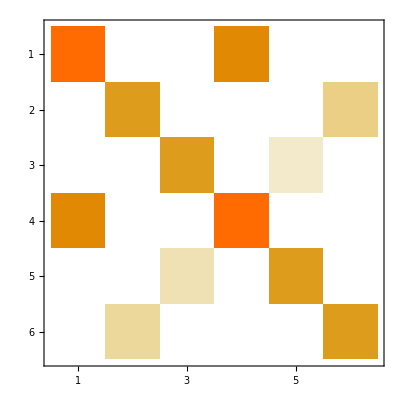

```mathematica
MatrixPlot[Abs@Chop@z012 ]
```

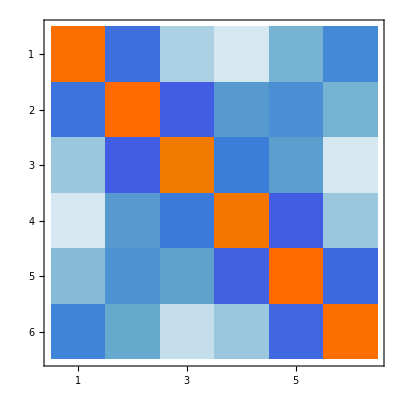

```mathematica
MatrixPlot[Im@Ymat ]
```

```mathematica
a= Exp[I 120 Degree];
A={{1,1,1},{1,a^2,a},{1,a,a^2}};
MatrixForm[A]
```

(1 | 1 | 1
1 | ⅇ^(240 ⅈ °) | ⅇ^(120 ⅈ °)
1 | ⅇ^(120 ⅈ °) | ⅇ^(240 ⅈ °))

```mathematica
(*
ℓ= 80.0;
Y1= 1/(Zpos ℓ) + Ypos ℓ;
Y2= -1/(Zpos ℓ);
 ZL= 376.32086209393407;
Y3= 1/ZL;
*)
```

```mathematica
Ztotal= Zmat 1000 30.0;
Yl=DiagonalMatrix[{1/200, 1/200, 1/200, 0.,0.,0.}];
A=IdentityMatrix[6];
B= Ztotal;
c = 0 A;
```

```mathematica
Q= ArrayFlatten[{{A, B},{c, A}}];
MatrixForm[Q]
```

(1 | 0 | 0 | 0 | 0 | 0 | 27.2818+26.4373 ⅈ | 3.11566+12.4111 ⅈ | 3.00827+10.9368 ⅈ | 3.00572+10.5222 ⅈ | 3.11024+11.2584 ⅈ | 3.26783+11.6224 ⅈ
0 | 1 | 0 | 0 | 0 | 0 | 3.11566+12.4111 ⅈ | 26.9663+26.7158 ⅈ | 2.87339+12.6289 ⅈ | 2.87252+11.4739 ⅈ | 2.96655+11.8938 ⅈ | 3.11024+11.2584 ⅈ
0 | 0 | 1 | 0 | 0 | 0 | 3.00827+10.9368 ⅈ | 2.87339+12.6289 ⅈ | 26.7841+26.8813 ⅈ | 2.78576+12.0586 ⅈ | 2.87252+11.4739 ⅈ | 3.00572+10.5222 ⅈ
0 | 0 | 0 | 1 | 0 | 0 | 3.00572+10.5222 ⅈ | 2.87252+11.4739 ⅈ | 2.78576+12.0586 ⅈ | 26.7841+26.8813 ⅈ | 2.87339+12.6289 ⅈ | 3.00827+10.9368 ⅈ
0 | 0 | 0 | 0 | 1 | 0 | 3.11024+11.2584 ⅈ | 2.96655+11.8938 ⅈ | 2.87252+11.4739 ⅈ | 2.87339+12.6289 ⅈ | 26.9663+26.7158 ⅈ | 3.11566+12.4111 ⅈ
0 | 0 | 0 | 0 | 0 | 1 | 3.26783+11.6224 ⅈ | 3.11024+11.2584 ⅈ | 3.00572+10.5222 ⅈ | 3.00827+10.9368 ⅈ | 3.11566+12.4111 ⅈ | 27.2818+26.4373 ⅈ
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

{6,6}

```mathematica
Va= 230./Sqrt[3];
Vb= Va Exp[I 120 Degree];
Vc= Va Exp[-I 120 Degree];
Ia1=Va1/200.;
Ib1= Vb1/200.;
Ic1 = Vc1/200.;
V0={Va, Vb, Vc, Va, Vb, Vc};
I0={Ia, Ib, Ic, 0,0,0};
V1={Va1,Vb1,Vc1,Vd1,Ve1,Vf1};
I1={Ia1,Ib1,Ic1,0,0,0};
```

```mathematica
recv=Join[V1,I1];
```

```mathematica
Q.recv
```

{(0.+0. ⅈ)+(1.13641+0.132186 ⅈ) Va1+(0.0155783+0.0620554 ⅈ) Vb1+(0.0150414+0.0546839 ⅈ) Vc1,(0.+0. ⅈ)+(0.0155783+0.0620554 ⅈ) Va1+(1.13483+0.133579 ⅈ) Vb1+(0.014367+0.0631446 ⅈ) Vc1,(0.+0. ⅈ)+(0.0150414+0.0546839 ⅈ) Va1+(0.014367+0.0631446 ⅈ) Vb1+(1.13392+0.134406 ⅈ) Vc1,(0.+0. ⅈ)+(0.0150286+0.0526109 ⅈ) Va1+(0.0143626+0.0573695 ⅈ) Vb1+(0.0139288+0.0602929 ⅈ) Vc1+Vd1,(0.+0. ⅈ)+(0.0155512+0.0562918 ⅈ) Va1+(0.0148328+0.0594688 ⅈ) Vb1+(0.0143626+0.0573695 ⅈ) Vc1+Ve1,(0.+0. ⅈ)+(0.0163392+0.0581121 ⅈ) Va1+(0.0155512+0.0562918 ⅈ) Vb1+(0.0150286+0.0526109 ⅈ) Vc1+Vf1,0.+0.005 Va1,0.+0.005 Vb1,0.+0.005 Vc1,0.,0.,0.}

```mathematica
Dimensions[%]
```

{12}

```mathematica
snd=Join[V0, I0]
```

{132.791,-66.3953+115. ⅈ,-66.3953-115. ⅈ,132.791,-66.3953+115. ⅈ,-66.3953-115. ⅈ,Ia,Ib,Ic,0,0,0}

```mathematica
Dimensions[%]
```

{12}

```mathematica
sol=Solve[snd==Q.recv,{ Vd,Ve,Vf,Ia,Ib,Ic,Va1,Vb1,Vc1, Vd1,Ve1,Vf1}]
```

{{Ia→0.593044-0.0396374 ⅈ,Ib→-0.263459+0.530219 ⅈ,Ic→-0.327572-0.488383 ⅈ,Va1→118.609-7.92749 ⅈ,Vb1→-52.6917+106.044 ⅈ,Vc1→-65.5144-97.6766 ⅈ,Vd1→132.455+0.689411 ⅈ,Ve1→-66.2609+115.169 ⅈ,Vf1→-66.1594-115.531 ⅈ}}

```mathematica
var={Ia,Ib,Ic,Va1,Vb1,Vc1,Vd1,Ve1,Vf1};
```

```mathematica
sol1=var/.Flatten[sol]
```

{0.593044-0.0396374 ⅈ,-0.263459+0.530219 ⅈ,-0.327572-0.488383 ⅈ,118.609-7.92749 ⅈ,-52.6917+106.044 ⅈ,-65.5144-97.6766 ⅈ,132.455+0.689411 ⅈ,-66.2609+115.169 ⅈ,-66.1594-115.531 ⅈ}

```mathematica
Abs[sol1]
```

{0.594368,0.592066,0.588066,118.874,118.413,117.613,132.457,132.87,133.134}

```mathematica
Arg[sol1]/π 180
```

{-3.8238,116.422,-123.851,-3.8238,116.422,-123.851,0.298215,119.913,-119.798}

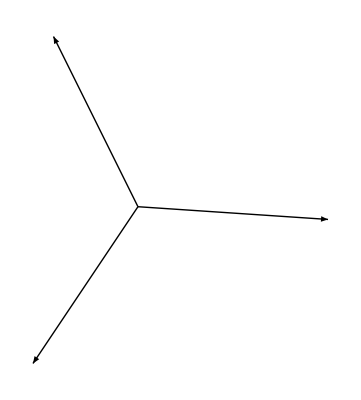

```mathematica
Graphics[{Arrow[{{0,0},{ Re[sol1[[1]]],Im[sol1[[1]]]}}],Arrow[{{0,0},{ Re[sol1[[2]]],Im[sol1[[2]]]}}],Arrow[{{0,0},{ Re[sol1[[3]]],Im[sol1[[3]]]}}]}]
```